# Neural Logic

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
?neurallogic`*
```

## Utilities

```mathematica
HardPrediction[m_]:=Ordering[(With[{t=#[True]},If[MissingQ[t],0,t]]&)/@Counts/@m,-1]
HardTarget[t_]:=Flatten[Position[t,True]]
HardResults[hardPredictionTargetPairs_]:=Module[{results,accuracy},
results=Reverse[Sort[Counts[{HardPrediction[First[#]][[1]],HardTarget[Last[#]][[1]]}&/@hardPredictionTargetPairs]]];
accuracy=KeySelect[results,First[#]==Last[#]&];
{"Accuracy = "<>ToString[Total[accuracy]/Length[hardPredictionTargetPairs]*100.0]<>"%",results}
]
```

```mathematica
HardPrediction[{{True,False,False},{False,False,False},{True,True,False}}]
```

{3}

```mathematica
HardPrediction[{{True,False,False},{True,False,False},{False,False,False}}]
```

{2}

```mathematica
HardPrediction[{{True,True,False},{True,False,False},{True,True,True}}]
```

Null

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=10;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->Soften[Boole[With[{r=bf@@x},{r,!r}]]]]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

1024

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,100,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralNAND[100,classificationLayerSize,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=4*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,45,RandomBalancedNormalSoftBits[#]&],
HardNeuralMajority[45,classificationLayerSize,RandomBalancedNormalSoftBits[#]&],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
softNet=NetGraph[<|"NeuralLogicNet"->net,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"}]
```

NetGraph[<>]

### Train net

```mathematica
{trainedNet,resultsObject}=NetTrain[softNet,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

```mathematica
trainedSoftNet=NetExtract[trainedNet,"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
resultsObject["RoundMeasurements"]
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
Column[HardResults[hardenedPredictionTargetPairs]]
```

<|Loss→0.0303399,ErrorRate→0.0004375|>

Accuracy = 99.95%
<|{2,2}→2002,{1,1}→1996,{2,1}→2|>

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 98.325%
<|{2,2}→2008,{1,1}→1925,{2,1}→61,{1,2}→6|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 26.4 kilobytes
Hard net size = 0.825 kilobytes
Saving factor = 32.

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"../data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{0,0,1,0},-Graphics-→{0,0,1,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0},-Graphics-→{0,1,0,0},-Graphics-→{0,0,1,0},-Graphics-→{1,0,0,0},-Graphics-→{0,0,1,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Standard neural net

```mathematica
ConvertDataToClasses[data_]:=MapAt[First[Flatten[Position[#,1]]]-1&,data,{All,2}]
```

### Create net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```

### Train net

```mathematica
result=NetTrain[net,ConvertDataToClasses[trainData],All,
ValidationSet->{ConvertDataToClasses[RandomSample[testData,UpTo[1000]]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate net

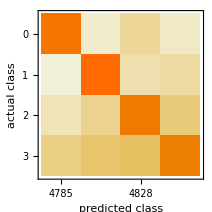
Classifier Measurements
Classifier method | Net
Number of test examples | 19803
Accuracy | (94.180.17) %
Accuracy baseline | (27.570.32) %
Geometric mean of probabilities | 0.449 ± 0.00065
Mean cross entropy | 0.802 ± 0.0014
Single evaluation time | 2.1 ms/example
Batch evaluation speed | 144. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]
```

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,100,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralAND[100,classificationLayerSize,RandomBalancedNormalSoftBits[#]&],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=32*numClasses},
HardNeuralChain[
{
HardNeuralNAND[inputSize,classificationLayerSize,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}
]
];
```

```mathematica
softNet=NetGraph[<|"NeuralLogicNet"->net,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"}];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[softNet,trainData,All,
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->4000];
```

```mathematica
trainedSoftNet=NetExtract[result["TrainedNet"],"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
(*ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]*)
```

```mathematica
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 92.7789%
<|{2,2}→5203,{1,1}→4483,{4,4}→4383,{3,3}→4304,{4,3}→280,{3,4}→251,{2,4}→166,{4,2}→160,{3,1}→132,{4,1}→110,{3,2}→95,{2,3}→90,{1,4}→67,{1,3}→60,{2,1}→18,{1,2}→1|>

```mathematica
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
```

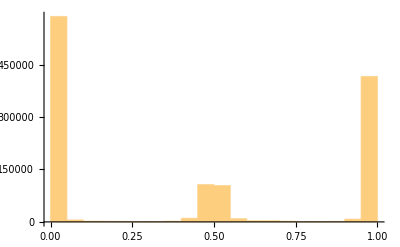

```mathematica
Histogram[Flatten[First/@softPredictionTargetPairs],PlotRange->All]
```

```mathematica
Histogram[Flatten[ExtractWeights[trainedSoftNet]],PlotRange->All]
```

-Graphics-

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 93.9858%
<|{2,2}→5167,{1,1}→4643,{4,4}→4410,{3,3}→4392,{3,4}→213,{2,4}→199,{4,3}→174,{2,3}→133,{4,2}→105,{1,3}→100,{1,4}→75,{3,2}→69,{4,1}→50,{3,1}→42,{2,1}→21,{1,2}→10|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 0.008 kilobytes
Hard net size = 0.00025 kilobytes
Saving factor = 32.

## Notes

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
NetFlatten[HardNeuralAND[2,4][[1]]]
```

NetGraph[<>]

```mathematica
f[x_List]:=Block[{min=Min[x],mean},
mean=Mean[x];
If[min>1/2,
min+(((min-1/2)mean)(1-min))^2,
min+((1/2-min)mean)^2]
]
```

```mathematica
Manipulate[
Plot[
{f[{x1,x2,x3,x4,x5}],x2,x3,x4,x5},
{x1,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic,PlotLegends->Automatic
],
{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1}
]
```

```mathematica
HardMinAll[]:=NetGraph[
<|
"Min"->AggregationLayer[Min],
"Mean"->AggregationLayer[Mean],
"Filter"->FunctionLayer[
If[#Min>1/2,
#Min+((#Min-1/2)#Mean)(1-#Min),
#Min+(1/2-#Min)#Mean
]&
]
|>,
{
"Min"->NetPort["Filter","Min"],
"Mean"->NetPort["Filter","Mean"]
}
]
```

```mathematica
hma=HardMinAll[]
```

NetGraph[<>]

```mathematica
hma[{{0.1,0.6,0.8},{0.9,0.9,0.52},{0.1,0.01,0.45},{0.1,0.01,0.55},{0.55,0.57,0.9}}]
```

{0.3,0.527424,0.101467,0.1178,0.56515}

## Counting

```mathematica
(* Experimental *)
net=With[{classificationLayerSize=32*numClasses},
NetGraph[
<|
"Layer1"->HardNeuralNAND[inputSize,600][[1]],
"Layer2"->HardNeuralNAND[600,classificationLayerSize][[1]],
"ToMatrix"->ReshapeLayer[{1,classificationLayerSize}],
"Require"->Require[HardNeuralLTEK[1,classificationLayerSize,32][[1]]][[1]],
"ToVector"->ReshapeLayer[{classificationLayerSize}],
"ClassPredictions"->HardNeuralPortLayer[classificationLayerSize,numClasses][[1]]
|>,
{
"Layer1"->"Layer2",
"Layer2"->"ToMatrix",
"ToMatrix"->"Require",
"Require"->"ToVector",
"ToVector"->"ClassPredictions"
}
]]
```